```mathematica
Forced Oscillators
Shwetabh Singh
MP2 - Project
```

```mathematica
Oscillator without Damping and Forcing
```

```mathematica
L =DSolve[{x'[t] ==y[t], y'[t] ==- b x[t]^3 -ω^2x[t]},{x[t], y[t]},{t,0,20}]
TraditionalForm[L]
```

{{y[t]→-1/(√2)(√(4 C[1]-2 ω^2 (InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(b/(ω^2-√(ω^4+4 b C[1]))) #1],(ω^2-√(ω^4+4 b C[1]))/(ω^2+√(ω^4+4 b C[1]))] √(1+(b #1^2)/(ω^2-√(ω^4+4 b C[1]))) √(1+(b #1^2)/(ω^2+√(ω^4+4 b C[1]))))/(√(b/(ω^2-√(ω^4+4 b C[1]))) √(4 C[1]-2 ω^2 #1^2-b #1^4))&][-t/(√2)+C[2]])^2-b (InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(b/(ω^2-√(ω^4+4 b C[1]))) #1],(ω^2-√(ω^4+4 b C[1]))/(ω^2+√(ω^4+4 b C[1]))] √(1+(b #1^2)/(ω^2-√(ω^4+4 b C[1]))) √(1+(b #1^2)/(ω^2+√(ω^4+4 b C[1]))))/(√(b/(ω^2-√(ω^4+4 b C[1]))) √(4 C[1]-2 ω^2 #1^2-b #1^4))&][-t/(√2)+C[2]])^4)),x[t]→InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(b/(ω^2-√(ω^4+4 b C[1]))) #1],(ω^2-√(ω^4+4 b C[1]))/(ω^2+√(ω^4+4 b C[1]))] √(1+(b #1^2)/(ω^2-√(ω^4+4 b C[1]))) √(1+(b #1^2)/(ω^2+√(ω^4+4 b C[1]))))/(√(b/(ω^2-√(ω^4+4 b C[1]))) √(4 C[1]-2 ω^2 #1^2-b #1^4))&][-t/(√2)+C[2]]},{y[t]→1/(√2)(√(4 C[1]-2 ω^2 (InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(b/(ω^2-√(ω^4+4 b C[1]))) #1],(ω^2-√(ω^4+4 b C[1]))/(ω^2+√(ω^4+4 b C[1]))] √(1+(b #1^2)/(ω^2-√(ω^4+4 b C[1]))) √(1+(b #1^2)/(ω^2+√(ω^4+4 b C[1]))))/(√(b/(ω^2-√(ω^4+4 b C[1]))) √(4 C[1]-2 ω^2 #1^2-b #1^4))&][t/(√2)+C[2]])^2-b (InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(b/(ω^2-√(ω^4+4 b C[1]))) #1],(ω^2-√(ω^4+4 b C[1]))/(ω^2+√(ω^4+4 b C[1]))] √(1+(b #1^2)/(ω^2-√(ω^4+4 b C[1]))) √(1+(b #1^2)/(ω^2+√(ω^4+4 b C[1]))))/(√(b/(ω^2-√(ω^4+4 b C[1]))) √(4 C[1]-2 ω^2 #1^2-b #1^4))&][t/(√2)+C[2]])^4)),x[t]→InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(b/(ω^2-√(ω^4+4 b C[1]))) #1],(ω^2-√(ω^4+4 b C[1]))/(ω^2+√(ω^4+4 b C[1]))] √(1+(b #1^2)/(ω^2-√(ω^4+4 b C[1]))) √(1+(b #1^2)/(ω^2+√(ω^4+4 b C[1]))))/(√(b/(ω^2-√(ω^4+4 b C[1]))) √(4 C[1]-2 ω^2 #1^2-b #1^4))&][t/(√2)+C[2]]}}

{{y(t)→-1/(√2)(√(-b (InverseFunction[-(ⅈ ⅈ sinh^-1(√(b/(ω^2-√(ω^4+4 b c_1))) #1)(ω^2-√(ω^4+4 b c_1))/(ω^2+√(ω^4+4 b c_1)) √((b #1^2)/(ω^2-√(ω^4+4 b c_1))+1) √((b #1^2)/(ω^2+√(ω^4+4 b c_1))+1))/(√(b/(ω^2-√(ω^4+4 b c_1))) √(-b #1^4-2 ω^2 #1^2+4 c_1))&][c_2-t/(√2)])^4-2 ω^2 (InverseFunction[-(ⅈ ⅈ sinh^-1(√(b/(ω^2-√(ω^4+4 b c_1))) #1)(ω^2-√(ω^4+4 b c_1))/(ω^2+√(ω^4+4 b c_1)) √((b #1^2)/(ω^2-√(ω^4+4 b c_1))+1) √((b #1^2)/(ω^2+√(ω^4+4 b c_1))+1))/(√(b/(ω^2-√(ω^4+4 b c_1))) √(-b #1^4-2 ω^2 #1^2+4 c_1))&][c_2-t/(√2)])^2+4 c_1)),x(t)→InverseFunction[-(ⅈ ⅈ sinh^-1(√(b/(ω^2-√(ω^4+4 b c_1))) #1)(ω^2-√(ω^4+4 b c_1))/(ω^2+√(ω^4+4 b c_1)) √((b #1^2)/(ω^2-√(ω^4+4 b c_1))+1) √((b #1^2)/(ω^2+√(ω^4+4 b c_1))+1))/(√(b/(ω^2-√(ω^4+4 b c_1))) √(-b #1^4-2 ω^2 #1^2+4 c_1))&][c_2-t/(√2)]},{y(t)→(√(-b (InverseFunction[-(ⅈ ⅈ sinh^-1(√(b/(ω^2-√(ω^4+4 b c_1))) #1)(ω^2-√(ω^4+4 b c_1))/(ω^2+√(ω^4+4 b c_1)) √((b #1^2)/(ω^2-√(ω^4+4 b c_1))+1) √((b #1^2)/(ω^2+√(ω^4+4 b c_1))+1))/(√(b/(ω^2-√(ω^4+4 b c_1))) √(-b #1^4-2 ω^2 #1^2+4 c_1))&][t/(√2)+c_2])^4-2 ω^2 (InverseFunction[-(ⅈ ⅈ sinh^-1(√(b/(ω^2-√(ω^4+4 b c_1))) #1)(ω^2-√(ω^4+4 b c_1))/(ω^2+√(ω^4+4 b c_1)) √((b #1^2)/(ω^2-√(ω^4+4 b c_1))+1) √((b #1^2)/(ω^2+√(ω^4+4 b c_1))+1))/(√(b/(ω^2-√(ω^4+4 b c_1))) √(-b #1^4-2 ω^2 #1^2+4 c_1))&][t/(√2)+c_2])^2+4 c_1))/(√2),x(t)→InverseFunction[-(ⅈ ⅈ sinh^-1(√(b/(ω^2-√(ω^4+4 b c_1))) #1)(ω^2-√(ω^4+4 b c_1))/(ω^2+√(ω^4+4 b c_1)) √((b #1^2)/(ω^2-√(ω^4+4 b c_1))+1) √((b #1^2)/(ω^2+√(ω^4+4 b c_1))+1))/(√(b/(ω^2-√(ω^4+4 b c_1))) √(-b #1^4-2 ω^2 #1^2+4 c_1))&][t/(√2)+c_2]}}

```mathematica
Manipulate[
Module[
{S1=NDSolve[{x'[t]==y[t],y'[t] == - b x[t]^3 -ω x[t], x[0]== 1,y[0]== 0},{x[t],y[t]},{t,0,100}]},Plot[Evaluate[x[t]/.S1],{t,0,100}, PlotRange->All]],{b,0,5}, {ω,0,5}]
```

Oscillator with Damping and Forcing

```mathematica
(*Phase Plot*)
Clear[Derivative]
Manipulate[
Module[
{S1=NDSolve[{x'[t]==y[t],y'[t] ==  F Sin[2t] - b x[t]^3 -x[t] -γ y[t], x[0]== 1,y[0]== 0},{x,y},{t,0,1000}]},ParametricPlot[Evaluate[{x[t],y[t]}/.S1],{t,0,1000}, PlotRange->All]],{γ,0,5},{b,0,5}, {F,0,5}]


(*Solution Plot*)
Clear[Derivative]
Manipulate[
Module[
{S1=NDSolve[{x'[t]==y[t],y'[t] ==  F Sin[2t] - b x[t]^3 -x[t] -γ y[t], x[0]== 1,y[0]== 0},{x,y},{t,0,1000}]},Plot[Evaluate[x[t]/.S1],{t,0,1000}, PlotRange->All]],{γ,0,5},{b,0,5}, {F,0,5}]


(*Frequency Plot*)
Clear[Derivative]
Manipulate[
Module[
{S1=NDSolve[{x'[t]==y[t],y'[t] ==  F Sin[2t] - b x[t]^3 -x[t] -γ y[t], x[0]== 1,y[0]== 0},{x,y},{t,0,1000}]},Plot[Evaluate[x[t]/.S1],{t,500,550}, PlotRange->All]],{γ,0,5},{b,0,5}, {F,0,5}]
```

```mathematica
(*Vector Plot*)
```

```mathematica
Manipulate[StreamPlot[{y,-γ y- x- b(x^3)},{x,-5,5},{y,-5,5}],{γ,-5,5},{b,-5,5}]
```

```mathematica
Fourier Transform
```

{{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>]}}}

{{√(2 π) x DiracDelta[k]→√(2 π) DiracDelta[k] InterpolatingFunction[{{0., 20.}}, <>],√(2 π) y DiracDelta[k]→√(2 π) DiracDelta[k] InterpolatingFunction[{{0., 20.}}, <>]}}

5

{1.,0.974364,0.929429,0.90481,0.922623,0.983604,1.06768,1.13888,1.15482,1.0791,0.891965,0.593254,0.198003,-0.268435,-0.767998,-1.23983,-1.59486,-1.73751,-1.61633,-1.256,-0.730615,-0.114563,0.534005,1.15242,1.64556,1.89361,1.81784,1.44258,0.868284,0.195699,-0.504639,-1.1665,-1.69048,-1.94909,-1.86062,-1.458,-0.854336,-0.157568,0.559431,1.22752,1.74197,1.97312,1.84753,1.41196,0.786472,0.0778961,-0.642384,-1.30217,-1.79119,-1.9808,-1.81084,-1.34276,-0.69999,0.0148628,0.732624,1.37748,1.83401,1.97715,1.76225,1.26431,0.607674,-0.110362,-0.822406,-1.44851,-1.86891,-1.96433,-1.70649,-1.18211,-0.514526,0.204438,0.90841,1.51299,1.89519,1.94346,1.64592,1.0988,0.422988,-0.294877,-0.988654,-1.56943,-1.91239,-1.91533,-1.58209,-1.01613,-0.334796,0.379925,1.06141,1.6165,1.92013,1.88068,1.51641,0.9357,0.251658,-0.457719,-1.12479,-1.65279,-1.91805,-1.84027,-1.45031,-0.859233,-0.17554}

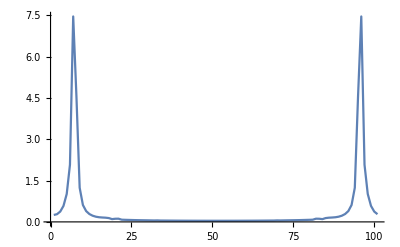

```mathematica
With[{F = 2.7, b= 0.7 , γ = 0.5},{S3= NDSolve[{x'[t]==y[t],y'[t] ==  F Sin[2t] - b x[t]^3 -x[t] -γ y[t], x[0]== 1,y[0]== 0},{x,y},{t,0,20}]}]
F= FourierTransform[S3,t, k] (* Just to see the interpolating function result*)
r = 5
data=Table[Evaluate[x[t]/.S3[[1]]],{t,0,20,1/r}]
ListLinePlot[Abs[Fourier[data]],PlotRange->All] (*Actual Fourier transform*)
```

```mathematica
Oscillator with Forcing and Quadratic  Damping
```

```mathematica
Clear[Derivative]
Manipulate[
Module[
{S2=NDSolve[{x'[t]==y[t],y'[t] ==  F Sin[2t] -x[t] -η y[t]Abs[y[t]], x[0]==1,y[0]== 0},{x,y},{t,0,1000}]},ParametricPlot[Evaluate[{x[t],y[t]}/.S2],{t,0,1000}, PlotRange->All]],{η,0,5}, {F,0,10}]
Clear[Derivative]
Manipulate[
Module[
{S2=NDSolve[{x'[t]==y[t],y'[t] ==  F Sin[2t] -x[t] -η y[t]Abs[y[t]], x[0]==1,y[0]== 0},{x,y},{t,0,1000}]},Plot[Evaluate[x[t]/.S2],{t,0,500}, PlotRange->All]],{η,0,5}, {F,0,10}]
```